```mathematica
GetParent[orgNo_]:=Module[{path,g,n,i},
Quiet[
path = StringForm["D:\\betterOutput\\organisms\\org``.json",orgNo];
{g,n,i}=Import[path//ToString];
"parent"/.i
]
]
GetLivingOrganisms[frameNo_]:=Module[{path,i,items,organisms},
path = StringForm["D:\\betterOutput\\output\\frame``.json",frameNo];
{i}=Import[path//ToString];
items = "Items"/.i;
organisms="o"/.items//DeleteDuplicates;
Select[organisms,#>=0&]
]
drawRelations[orgs_,steps_]:=Module[{g,gs},
gs=NestGraph[If[#<0,-1,GetParent[#]]&,#,steps]&/@orgs;
g=GraphUnion@@gs;
HighlightGraph[g,gs,VertexLabels->"Name"]
]
stepsToLCA[a_,b_]:=Module[{lA={a},lB={b}},
While[ContainsNone[lA,lB],
AppendTo[lA,GetParent[Last[lA]]];
AppendTo[lB,GetParent[Last[lB]]];
];
Min[Length[lA],Length[lB]]-1
]
```

```mathematica
step=848700;
```

```mathematica
living=GetLivingOrganisms[step];
```

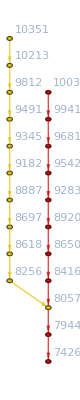

```mathematica
With[{pair=RandomChoice[living,2]},drawRelations[pair,stepsToLCA@@pair]]
```

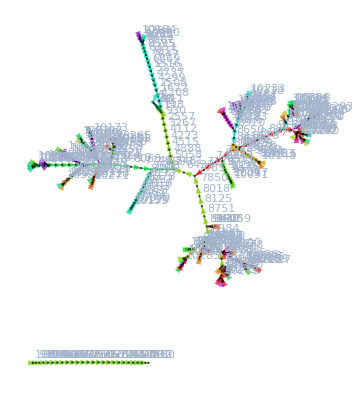

```mathematica
g=drawRelations[living,25]
```

```mathematica
findSpecies[pool_]:=Module[{orgs = pool,definingSpecimen,s,species={}},
While[Length[orgs]>0,
definingSpecimen=RandomChoice[orgs];
(*orgs=DeleteCases[orgs,definingSpecimen];*)
s=Select[orgs,stepsToLCA[#,definingSpecimen]<5&];
AppendTo[species,s];
orgs=Complement[orgs,s];
PrintTemporary[orgs//Length];
];
species
];
species=findSpecies[living];
```

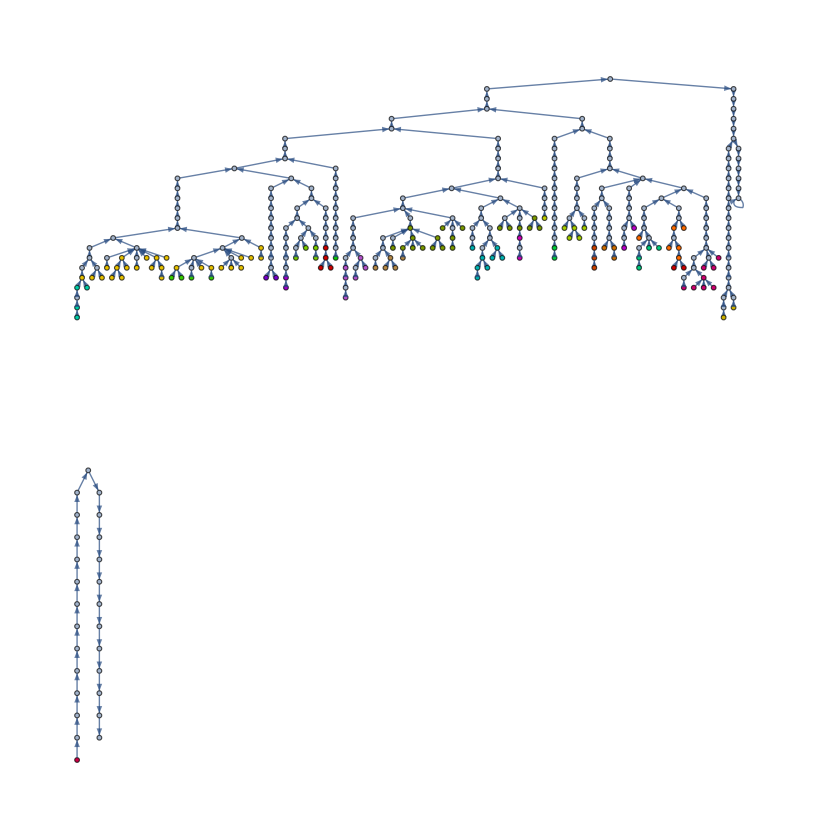

```mathematica
HighlightGraph[Graph[EdgeList[g],GraphLayout->"LayeredEmbedding",VertexLabels->Placed["Name",Tooltip]],species]
```

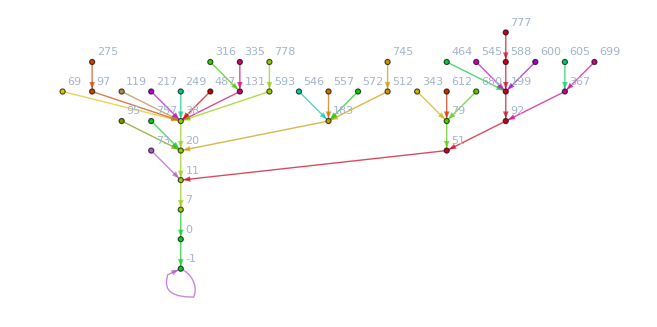

```mathematica
drawRelations[%,5]
```

```mathematica
a={1,2,3,4,5};
a=DeleteCases[a,{3,4,1}];
a
```

{1,2,3,4,5}

```mathematica
stepsToLCA[#,15]<200&/@Range[0,20]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Cases[Range[0,20],stepsToLCA[#,15]&<200]
```

{}